```mathematica
(*Definition of qubit functions*)

(*Eq. (31) with N=n, k1=k, k0=n-k, we ignore the minimum here, because we restrict ourselves to cases with k < n-k*)
e[k_]=(n!(n-k)!k!)/(n^n(n-k)^(n-k)k^k)k;

(*Eq. (32) with N=n, k1=k, k0=n-k*)
f[k_]=(n!k!)/((n-k)!)((n-k)^(n-k)k^k)/n^(n+2k)(k!)/k^k n;
```

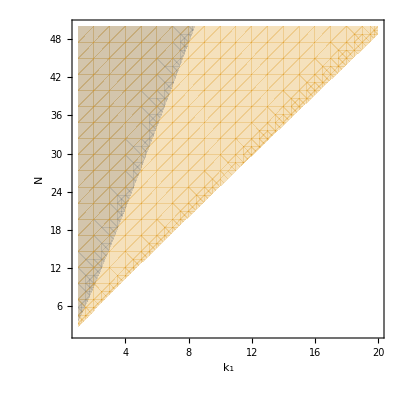

```mathematica
(*Plot the regions where Eq. (32) >= Eq. (10), and Eq. (32) >= Eq. (31)*)
plot11=RegionPlot[{Piecewise[{{(n!/n^n)-f[k]<=0,k<n-k}}],Piecewise[{{e[k]-f[k]<=0,k<n-k}}]},{k,1,20},{n,2,50},BoundaryStyle->None,FrameLabel->{Subscript[k, 1],N},LabelStyle->{Black,16}]
```

FittedModel[0.698508+2.41059 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.698508 | 0.0560971 | 12.4518 | 2.77726×10^-10
x | 2.41059 | 0.00468289 | 514.765 | 5.70834×10^-39

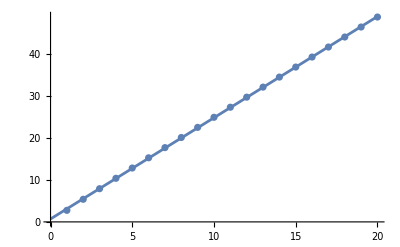

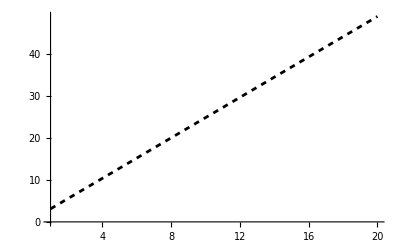

```mathematica
(*Find the values for which Eq. (31) = Eq. (32)*)
For[i=1,i<=20,i++,
T[i]={i,n}/.FindRoot[e[i]==f[i],{n,i+1}]]
A=Array[T[#]&,20];

(*Fit a linear function to the found values*)
fit=LinearModelFit[A,x,x]
fit["ParameterTable"]
plot311=Show[Plot[fit[x],{x,0,20}],ListPlot[A]]
plot31=Plot[fit[x],{x,1,20},PlotStyle->{Black,Dashing[0.01,0.01]}]
```

FittedModel[-3.57804+6.37539 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -3.57804 | 0.341601 | -10.4743 | 5.99936×10^-6
x | 6.37539 | 0.055054 | 115.802 | 3.45576×10^-14

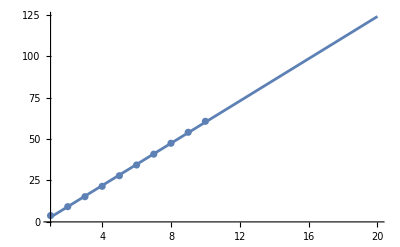

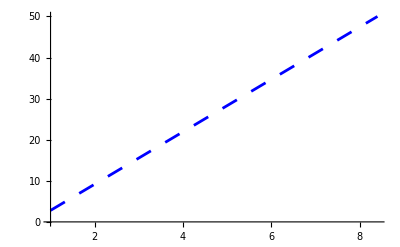

```mathematica
(*Find the values for which Eq. (10) = Eq. (32)*)
For[i=1,i<=10,i++,
T2[i]={i,n}/.FindRoot[(n!/n^n)==f[i],{n,i+1},MaxIterations->250]]
A2=Array[T2[#]&,10];
(*Fit a linear function to the found values*)
fit2=LinearModelFit[A2,x,x]
fit2["ParameterTable"]
plot211=Show[Plot[fit2[x],{x,1,20}],ListPlot[A2]]
plot21=Plot[fit2[x],{x,1,10},PlotStyle->{Blue,Dashing[0.03,0.05,0.03]},PlotRange->{All,{0,50}}]
```

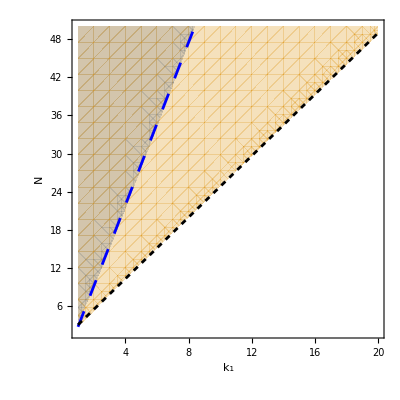

```mathematica
(*Plot the region plot and the fit functions in one graph*)
s2=Show[plot11,plot21,plot31]
(*Export["ContourPlotQubit.pdf",%]*)
```

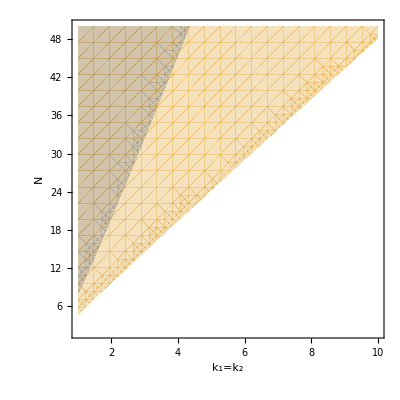

```mathematica
(*Definition of qutrit functions*)

(*Eq. (35) with N=n, k2=k2, k1=k, k0=n-k1-k2, we ignore the minimum here, because we restrict ourselves to cases with k1 = k2 < n-k1-k2*)
e2[k1_,k2_]=(n!(n-k1-k2)!k1!k2!)/(n^n(n-k1-k2)^(n-k1-k2)k1^k1 k2^k2)k2;

(*Eq. (36) with N=n, k2=k2, k1=k, k0=n-k1-k2*)
f2[k1_,k2_]=(n!(k1+k2)!)/((n-k1-k2)!)((n-k1-k2)^(n-k1-k2)(k1+k2)^(k1+k2))/n^(n+2(k1+k2))(k1!k2!)/(k1^k1 k2^k2)n;

(*Plot the regions where Eq. (36) >= Eq. (10), and Eq. (36) >= Eq. (35)*)
plot12=RegionPlot[{Piecewise[{{(n!/n^n)-f2[k,k]<=0,k<n-2k}}],Piecewise[{{e2[k,k]-f2[k,k]<=0,k<n-2k}}]},{k,1,10},{n,2,50},BoundaryStyle->None,FrameLabel->{"k_1=k_2",N},LabelStyle->{Black,16}]
```

FittedModel[0.148443+4.8134 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.148443 | 0.0706711 | 2.10048 | 0.0688864
x | 4.8134 | 0.0113897 | 422.61 | 1.10059×10^-18

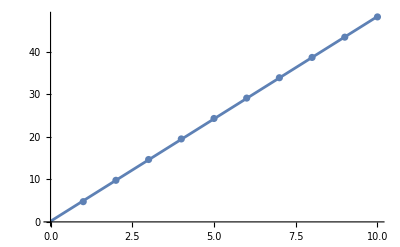

```mathematica
(*Find the values for which Eq. (36) = Eq. (35)*)
For[i=1,i<=10,i++,
T[i]={i,n}/.FindRoot[e2[i,i]==f2[i,i],{n,2i+1},MaxIterations->250]]
A=Array[T[#]&,10];

(*Fit a linear function to the found values*)
fit=LinearModelFit[A,x,x]
fit["ParameterTable"]
plot321=Show[Plot[fit[x],{x,0,10}],ListPlot[A]]
plot32=Plot[fit[x],{x,1,10},PlotStyle->{Black,Dashing[0.01,0.01]}];
```

FittedModel[-5.14002+12.6813 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -5.14002 | 0.440452 | -11.6699 | 0.00135179
x | 12.6813 | 0.132801 | 95.491 | 2.5317×10^-6

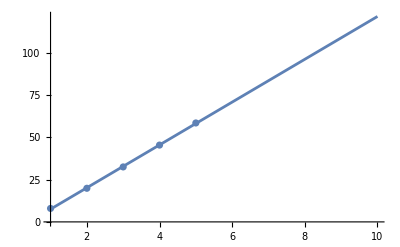

```mathematica
(*Find the values for which Eq. (36) = Eq. (10)*)
For[i=1,i<=5,i++,
T2[i]={i,n}/.FindRoot[(n!/n^n)==f2[i,i],{n,10i-2},MaxIterations->250]]
A2=Array[T2[#]&,5];

(*Fit a linear function to the found values*)
fit2=LinearModelFit[A2,x,x]
fit2["ParameterTable"]
plot221=Show[Plot[fit2[x],{x,1,10}],ListPlot[A2]]
plot22=Plot[fit2[x],{x,1,10},PlotStyle->{Blue,Dashing[0.03,0.05,0.03]},PlotRange->{All,{0,50}}];
```

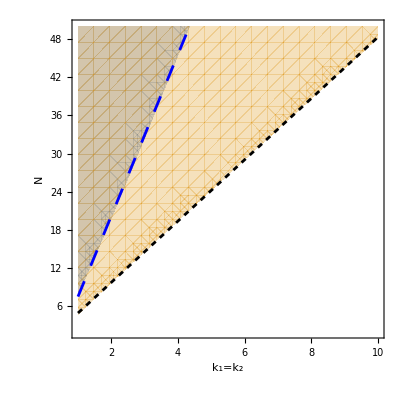

```mathematica
s3=Show[plot12,plot22,plot32]
Export["ContourPlotQutrit.pdf",%]
```

```mathematica
(*"ContourPlotQutrit.pdf"*)
```